```mathematica
Ratio1[βr_]:=( Sqrt[1.0-βr^2]);
Brake1[t_,τ_,βr_]:=βr*((1+Tanh[20t])/2-(1+Tanh[20(t-τ)])/2);
Brake2[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
η = Ratio1[(Brake2[t,τ0 ,τ ,Subscript[β, r]])];

Slip angle;
Subscript[α, sl1]=ArcTan[3η*Subscript[μ, 1] Subscript[F, z1]/Subscript[C, α1]]/.rules;Subscript[α, sl2]=ArcTan[3η*Subscript[μ, 2] Subscript[F, z2]/Subscript[C, α2]]/.rules;
Subscript[α, sl3]=ArcTan[3η*Subscript[μ, 3] Subscript[F, z3]/Subscript[C, α3]]/.rules;Subscript[α, sl4]=ArcTan[3η*Subscript[μ, 4] Subscript[F, z4]/Subscript[C, α4]]/.rules;

Subscript[α, 1]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.vRule/.rules;
Subscript[α, 2]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.vRule/.rules;Subscript[α, 3]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])/.rules;Subscript[α, 4]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])/.rules;

Tire  Force;
Subscript[f, y1]=Piecewise[{{ -Subscript[C, α1]Tan[Subscript[α, 1]]+ ((Subscript[C, α1])^2/(3η*Subscript[μ, 1] Subscript[F, z1]) Abs[Tan[Subscript[α, 1]]] Tan[Subscript[α, 1]])- ((Subscript[C, α1])^3/(27((η)^2 Subscript[μ, 1] Subscript[F, z1])^2)(Tan[Subscript[α, 1]])^3),(Abs[Subscript[α, 1]])<Subscript[α, sl1]},{-η Subscript[μ, 1] Subscript[F, z1] Sign[Subscript[α, 1]],(Abs[Subscript[α, 1]])≥Subscript[α, sl1]}}]/.rules;
Subscript[f, y2]=Piecewise[{{ -Subscript[C, α2] Tan[Subscript[α, 2]]+ ((Subscript[C, α2])^2/(3η*Subscript[μ, 2] Subscript[F, z2]) Abs[Tan[Subscript[α, 2]]] Tan[Subscript[α, 2]])- ((Subscript[C, α2])^3/(27(η^2 Subscript[μ, 2] Subscript[F, z2])^2)(Tan[Subscript[α, 2]])^3),(Abs[Subscript[α, 2]])<Subscript[α, sl2]},{-η Subscript[μ, 2] Subscript[F, z2] Sign[Subscript[α, 2]],(Abs[Subscript[α, 2]])≥Subscript[α, sl2]}}]/.rules;
Subscript[f, y3]=Piecewise[{{-Subscript[C, α3] Tan[Subscript[α, 3]]+ ((Subscript[C, α3])^2/(3η*Subscript[μ, 3] Subscript[F, z3]) Abs[Tan[Subscript[α, 3]]] Tan[Subscript[α, 3]])- ((Subscript[C, α3])^3/(27(η^2 Subscript[μ, 3] Subscript[F, z3])^2)(Tan[Subscript[α, 3]])^3),(Abs[Subscript[α, 3]])<Subscript[α, sl3]},{ -η Subscript[μ, 3] Subscript[F, z3] Sign[Subscript[α, 3]],(Abs[Subscript[α, 3]])≥Subscript[α, sl3]}}]/.rules;
Subscript[f, y4]=Piecewise[{{-Subscript[C, α4] Tan[Subscript[α, 4]]+ ((Subscript[C, α4])^2/(3η*Subscript[μ, 4] Subscript[F, z4]) Abs[Tan[Subscript[α, 4]]] Tan[Subscript[α, 4]])- ((Subscript[C, α4])^3/(27(η^2 Subscript[μ, 4] Subscript[F, z4])^2)(Tan[Subscript[α, 4]])^3),(Abs[Subscript[α, 4]])<Subscript[α, sl4]},{-η Subscript[μ, 4] Subscript[F, z4] Sign[Subscript[α, 4]],(Abs[Subscript[α, 4]])≥Subscript[α, sl4]}}]/.rules;

Subscript[F, x1] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 1] Subscript[F, z1] Cos[δ] - Subscript[f, y1] Sin[δ]/.vRule/.rules;
Subscript[F, x2] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 2] Subscript[F, z2] Cos[δ] - Subscript[f, y2] Sin[δ]/.vRule/.rules;
Subscript[F, x3] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 3] Subscript[F, z3] Cos[0] - Subscript[f, y3] Sin[0]/.rules;
Subscript[F, x4] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 4] Subscript[F, z4] Cos[0] - Subscript[f, y4] Sin[0]/.rules;

Subscript[F, y1] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 1] Subscript[F, z1] Sin[δ] + Subscript[f, y1] Cos[δ]/.vRule/.rules;
Subscript[F, y2] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 2] Subscript[F, z2] Sin[δ] + Subscript[f, y2] Cos[δ]/.vRule/.rules;
Subscript[F, y3] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 3] Subscript[F, z3] Sin[0] + Subscript[f, y3] Cos[0]/.rules;
Subscript[F, y4] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 4] Subscript[F, z4] Sin[0] + Subscript[f, y4] Cos[0]/.rules;

Eq1 = m D[x[t],{t,2}] == m D[y[t],{t,1}]D[ψ[t],{t,1}] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules;
Eq2 = m D[y[t],{t,2}] == -m D[x[t],{t,1}] D[ψ[t],{t,1}] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules;
Eq3 =Subscript[J, z] D[ψ[t],{t,2}] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r]*(Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)(-Subscript[F, x1] + Subscript[F, x2] - Subscript[F, x3] + Subscript[F, x4])/.rules;
Eq4 = m D[Subscript[e, ψ][t],{t,1}]==m D[ψ[t],{t,1}]-m D[Subscript[ψ, d][t],{t,1}]/.vRule2/.rules;
Eq5 = m D[Subscript[e, y][t],{t,1}]==m D[y[t],{t,1}] Cos[Subscript[e, ψ][t]] + m D[x[t],{t,1}]Sin[Subscript[e, ψ][t]]/.rules;

rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]-> -0.1,Subscript[K, ψ]-> -1.1,Subscript[ψ, d1] ->0.12,Subscript[t, lp] -> 0.5
};

time = 49;

τ0 = {0,10,20,50};
τ = {5,5,5,5};
Subscript[β, r]={0.1,0.5,-0.5,-0.1};
vRule2 = {Subscript[ψ, d][t]->Mod[ArcCos[x[t]/(Subscript[t, lp] Sqrt[D[x[t],t]^2+D[y[t],t]^2])],Pi/2]/.rules};
vRule={δ->(Subscript[K, y] Subscript[e, y][t]+Subscript[K, ψ] Subscript[e, ψ][t]+Subscript[K, ψ] Subscript[ψ, d][t]-Subscript[K, ψ] Subscript[ψ, d1])/.vRule2/.rules};

initCond={x[0]==0.1,x'[0]==0.1,y[0]==0.1,y'[0]==0.01,ψ[0]==0.01,ψ'[0]==0.01,Subscript[e, y][0]==0.08,Subscript[e, ψ][0]==0.1};

solution2=NDSolve[{Eq1,Eq2,Eq3,Eq4,Eq5,initCond},{x,y,ψ,Subscript[e, y],Subscript[e, ψ]},{t,0,time}]

Plot[Evaluate[{x[t],y[t]}/.solution2],{t,0,time},Frame->True,FrameLabel->{"t","x,y"},PlotLegends->{"x(t)","y(t)"},PlotRange->All] 
Plot[Evaluate[{x'[t],y'[t]}/.solution2],{t,0,time},Frame->True,FrameLabel->{"t","v_x,v_y"},PlotLegends->{"v_x(t)","v_y(t)"},PlotRange->All] 
Plot[Evaluate[{x''[t],y''[t]}/.solution2],{t,0,time},Frame->True,FrameLabel->{"t","a_x,a_y"},PlotLegends->{"a_x(t)","a_y(t)"},PlotRange->All] 
Plot[Evaluate[{η}/.solution2],{t,0,time},Frame->True,FrameLabel->{"t","η"},PlotLegends->{"η"},PlotRange->All] 
Plot[Evaluate[{δ/.vRule}/.solution2],{t,0,time},Frame->True,FrameLabel->{"t","δ"},PlotLegends->{"δ"},PlotRange->All]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution2],{t,0,time},PlotRange-> All]
```

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

NDSolve[{2050. x''[t]==-2 (Piecewise[{{80000. Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}]) Sin[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]]+42590. (-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+53438. Cos[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+2050. y'[t] ψ'[t],2050. y''[t]==2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+2 Cos[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))-2050. x'[t] ψ'[t],3344. ψ''[t]==0.-2.94 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+1.43 (2 Cos[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.132+1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.132-1.1 Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]-0.1 e_y[t]-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-55+t)])+1/2 (1+Tanh[20 (-50+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))),2050. e_ψ'[t]==2050. ψ'[t]-2050. ψ_d'[t],2050. e_y'[t]==2050. Sin[e_ψ[t]] x'[t]+2050. Cos[e_ψ[t]] y'[t],{x[0]==0.1,x'[0]==0.1,y[0]==0.1,y'[0]==0.01,ψ[0]==0.01,ψ'[0]==0.01,e_y[0]==0.08,e_ψ[0]==0.1}},{x,y,ψ,e_y,e_ψ},{t,0,49}]

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001001 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.001 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {e_y[t], e_ψ[t], ψ_d[t], x[t], y[t], ψ[t]}, than equations, so the system is underdetermined.

-Graphics-

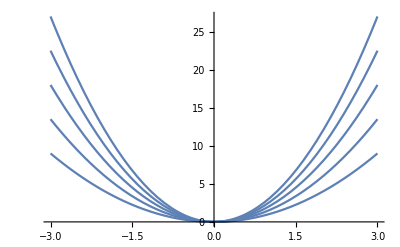

```mathematica
g[x_,y_,γ_]:=γ x^2+y
Plot3D[Table[g[x,γ],{γ,1,3,.5}],{x,-3,3},Plot]
```

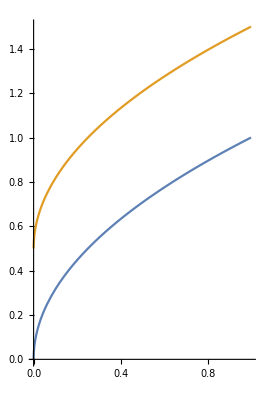

```mathematica
ParametricPlot[{{t,t^(1/2)},{t,t^(1/2)+.5}},{t,0,1}]
```

```mathematica
Eq1 = m D[x[t],{t,2}] == m D[y[t],{t,1}]D[ψ[t],{t,1}] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules
```

2050. x''[t]==-2 (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}]) Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]]+42590. (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+53438. Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+2050. y'[t] ψ'[t]

```mathematica
Eq2 = m D[y[t],{t,2}] == -m D[x[t],{t,1}] D[ψ[t],{t,1}] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules
```

2050. y''[t]==0.+2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+2 Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))-2050. x'[t] ψ'[t]

```mathematica
Eq3 =Subscript[J, z] D[ψ[t],{t,2}] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r]*(Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)(-Subscript[F, x1] + Subscript[F, x2] - Subscript[F, x3] + Subscript[F, x4])/.rules
```

3344. ψ''[t]==0.-1.47 (0.+2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}]))+1.43 (2 Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t]))))

```mathematica
Eq4 = m D[Subscript[e, ψ][t],{t,1}]==m D[ψ[t],{t,1}]-m D[Subscript[ψ, d][t],{t,1}]/.variableRules2/.rules
```

2050. e_ψ'[t]==2050. ψ'[t]-2050. (ψ'[t]-e_ψ'[t])

```mathematica
Eq5 = m D[Subscript[e, y][t],{t,1}]==m D[y[t],{t,1}] Cos[Subscript[e, ψ][t]] + m D[x[t],{t,1}]Sin[Subscript[e, ψ][t]]/.rules//Simplify
```

1. Sin[e_ψ[t]] x'[t]+1. Cos[e_ψ[t]] y'[t]==1. e_y'[t]

```mathematica
Subscript[ψ, d]->(FunctionExpand[Mod[ArcCos[x[t]/(Subscript[t, lp] Sqrt[D[x[t],t]^2+D[y[t],t]^2])],Pi/2]])/.rules
```

ψ_d→Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]

```mathematica
Subscript[ψ, d]->(FullSimplify[Mod[ArcCos[x[t]/(Subscript[t, lp] Sqrt[D[x[t],t]^2+D[y[t],t]^2])],Pi/2]])/.rules
```

ψ_d→Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]

```mathematica
Subscript[ψ, d]->(Solve[Mod[ArcCos[x[t]/(Subscript[t, lp] Sqrt[D[x[t],t]^2+D[y[t],t]^2])],Pi/2]])/.rules
```

Solve::naqs: ArcCos[x[t]/t_lp √SuperscriptBox[ is not a quantified system of equations and inequalities.

Solve::naqs: ArcCos[2.` x[t]/√SuperscriptBox[ is not a quantified system of equations and inequalities.

ψ_d→Solve[Mod[ArcCos[(2. x[t])/(√(x'[t]^2+y'[t]^2))],π/2]]